```mathematica
Series[1/2/λ/l^2(1-Sqrt[1-4λ(1-(rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ) z^4+(k rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ])^2 z^6)])/.{k->Sqrt[8Pi],rp->1/zp},{λ,0,1}]//Normal//FullSimplify
```

(9 (z^4-zp^4) (z^4 λ-zp^4 (1+λ))-48 l^2 π z^4 (z-zp) (z+zp) (2 z^4 λ-zp^4 (1+3 λ)) μ^2+256 l^4 π^2 z^8 (z^2-zp^2)^2 λ μ^4)/(9 l^2 zp^8)

```mathematica
Series[1/2/λ/l^2(1-Sqrt[1-4λ(1-z[t]^4(1/zp^4+32Pi μ^2l^2/(3(1+Sqrt[1-4λ])zp^2))+32Pi μ^2l^2/(3(1+Sqrt[1-4λ]))z[t]^6/zp^4)]),{λ,0,1}]
```

(3 zp^4-3 z[t]^4-16 l^2 π zp^2 μ^2 z[t]^4+16 l^2 π μ^2 z[t]^6)/(3 l^2 zp^4)+((-(64 l^2 π μ^2 (zp^2 z[t]^4-z[t]^6))/(3 zp^4)+1/4 (-4+(4 z[t]^4)/zp^4+(64 l^2 π μ^2 z[t]^4)/(3 zp^2)-(64 l^2 π μ^2 z[t]^6)/(3 zp^4))^2) λ)/(4 l^2)+O[λ]^2

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
EulerEquations[-1/z [t]Sqrt[((3 zp^4-3 z[t]^4-16 l^2 π zp^2 μ^2 z[t]^4+16 l^2 π μ^2 z[t]^6)/(3 l^2 zp^4)+((-(64 l^2 π μ^2 (zp^2 z[t]^4-z[t]^6))/(3 zp^4)+1/4 (-4+(4 z[t]^4)/zp^4+(64 l^2 π μ^2 z[t]^4)/(3 zp^2)-(64 l^2 π μ^2 z[t]^6)/(3 zp^4))^2) λ)/(4 l^2))(1/2(1+Sqrt[1-4λ]))-z'[t]^2/((3 zp^4-3 z[t]^4-16 l^2 π zp^2 μ^2 z[t]^4+16 l^2 π μ^2 z[t]^6)/(3 l^2 zp^4)+((-(64 l^2 π μ^2 (zp^2 z[t]^4-z[t]^6))/(3 zp^4)+1/4 (-4+(4 z[t]^4)/zp^4+(64 l^2 π μ^2 z[t]^4)/(3 zp^2)-(64 l^2 π μ^2 z[t]^6)/(3 zp^4))^2) λ)/(4 l^2))]+q μ (1-z[t]^2/zp^2),z[t],t]
```

-(2 q μ z[t])/zp^2+(36 l^2 zp^8 z[t]^2 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) z'[t]^2)/((zp^2-z[t]^2)^2 (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)^2 √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))+(9 l^2 zp^8 z'[t]^2)/(z[t]^2 (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10) √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))-(z[t]^2 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) (1+√(1-4 λ)+(162 l^4 zp^16 z'[t]^2)/((zp^2-z[t]^2)^2 (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)^2)))/(9 l^2 zp^8 √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))+1/z[t]^2(√(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))-(9 l^2 zp^8 z''[t])/(z[t] (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10) √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))+(9 l^2 zp^8 z'[t] (1/(9 l^2 zp^8)2 (1+√(1-4 λ)) z[t]^3 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) z'[t]+(36 l^2 zp^8 z[t]^3 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) z'[t]^3)/((zp^2-z[t]^2)^2 (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)^2)-(18 l^2 zp^8 z'[t] z''[t])/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))/(2 z[t] (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10) (1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)))^(3/2))==0

```mathematica
qcrit[zs_,zp_,μ_,l_,λ_]:=Sqrt[1-zs^4/zp^4+(16 π zs^6 μ^2)/(3 zp^4)-(16 π zs^4 μ^2)/(3 zp^2)]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
μextreme[l_,zh_,λ_]:=1/2/l/zh Sqrt[3/8/Pi](1+Sqrt[1-4λ]);
f[z_,zp_,μ_,l_,λ_]:=(9 (z^4-zp^4) (z^4 λ-zp^4 (1+λ))-48 l^2 π z^4 (z-zp) (z+zp) (2 z^4 λ-zp^4 (1+3 λ)) μ^2+256 l^4 π^2 z^8 (z^2-zp^2)^2 λ μ^4)/(9 l^2 zp^8);
zm1[q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=NDSolveValue[
{-(2 q μ z[t])/zp^2+(36 l^2 zp^8 z[t]^2 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) z'[t]^2)/((zp^2-z[t]^2)^2 (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)^2 √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))+(9 l^2 zp^8 z'[t]^2)/(z[t]^2 (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10) √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))-(z[t]^2 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) (1+√(1-4 λ)+(162 l^4 zp^16 z'[t]^2)/((zp^2-z[t]^2)^2 (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)^2)))/(9 l^2 zp^8 √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))+1/z[t]^2(√(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))-(9 l^2 zp^8 z''[t])/(z[t] (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10) √(1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))+(9 l^2 zp^8 z'[t] (1/(9 l^2 zp^8)2 (1+√(1-4 λ)) z[t]^3 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) z'[t]+(36 l^2 zp^8 z[t]^3 (-3 zp^4 (3+16 l^2 π zp^2 μ^2+6 λ (1+8 l^2 π zp^2 μ^2))+72 l^2 π zp^4 (1+3 λ) μ^2 z[t]^2+2 λ (3+16 l^2 π zp^2 μ^2)^2 z[t]^4-80 l^2 π λ μ^2 (3+16 l^2 π zp^2 μ^2) z[t]^6+768 l^4 π^2 λ μ^4 z[t]^8) z'[t]^3)/((zp^2-z[t]^2)^2 (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)^2)-(18 l^2 zp^8 z'[t] z''[t])/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10))))/(2 z[t] (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10) (1/(18 l^2 zp^8)(1+√(1-4 λ)) (zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)-(9 l^2 zp^8 z'[t]^2)/((zp^2-z[t]^2) (9 zp^6 (1+λ)+9 zp^4 (1+λ) z[t]^2-3 (3 zp^2 λ+16 l^2 π zp^4 (1+3 λ) μ^2) z[t]^4-9 λ z[t]^6+32 l^2 π λ μ^2 (3+8 l^2 π zp^2 μ^2) z[t]^8-256 l^4 π^2 λ μ^4 z[t]^10)))^(3/2))==0/.{q->q1,zp->zp1,μ->μ1,l->l1,λ->λ1},z[0]== zs1,z'[0]==0},z,{t,0.01,3},Method->"BDF"
];
fz1[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=zm1[q1,zp1,zs1,μ1,l1,λ1][t1];
dfz1[t_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=D[fz1[t1,q1,zp1,zs1,μ1,l1,λ1],t1]/.{t1->t};
pz[t1_,q1_,zp1_,zs1_,μ1_,l1_,λ1_]:=Block[
{zd,z2,fz,n1},
z2=fz1[t1,q1,zp1,zs1,μ1,l1,λ1];
fz=f[z2,zp1,μ1,l1,λ1];
zd=dfz1[t1,q1,zp1,zs1,μ1,l1,λ1];
n1=Sqrt[(1+Sqrt[1-4λ1])/2];
Return[1/z2/fz zd/Sqrt[n1^2fz-zd^2/fz]];
];
```

```mathematica
0.75μextreme[1,1,0]
```

0.259121

```mathematica
qcrit[0.1,1,0.75μextreme[1,1,0],1,0]
```

42.8755

```mathematica
zm1[1,0.1qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.75μextreme[1,1,0],1,1,0]
```

InterpolatingFunction[…]

```mathematica
Table[{i,Abs[fz1[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.75μextreme[1,1,0],1,1,0]]},{i,0.01,3,0.05}]
```

{{0.01,0.259313},{0.06,0.265962},{0.11,0.281444},{0.16,0.304382},{0.21,0.333181},{0.26,0.366367},{0.31,0.402717},{0.36,0.441255},{0.41,0.481196},{0.46,0.521892},{0.51,0.562782},{0.56,0.603364},{0.61,0.643179},{0.66,0.681807},{0.71,0.718866},{0.76,0.754025},{0.81,0.787007},{0.86,0.817604},{0.91,0.845679},{0.96,0.871165},{1.01,0.894069},{1.06,0.914455},{1.11,0.932441},{1.16,0.948182},{1.21,0.961857},{1.26,0.97366},{1.31,0.983789},{1.36,0.992437},{1.41,0.99979},{1.46,1.00602},{1.51,1.01127},{1.56,1.0157},{1.61,1.01941},{1.66,1.02253},{1.71,1.02514},{1.76,1.02731},{1.81,1.02913},{1.86,1.03065},{1.91,1.03191},{1.96,1.03296},{2.01,1.03384},{2.06,1.03457},{2.11,1.03517},{2.16,1.03567},{2.21,1.03609},{2.26,1.03644},{2.31,1.03673},{2.36,1.03697},{2.41,1.03716},{2.46,1.03733},{2.51,1.03747},{2.56,1.03758},{2.61,1.03767},{2.66,1.03775},{2.71,1.03782},{2.76,1.03787},{2.81,1.03792},{2.86,1.03795},{2.91,1.03798},{2.96,1.03801}}

```mathematica
Table[{i,Abs[pz[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.75μextreme[1,1,0],1,1,0]]//Log},{i,0.01,3,0.05}]
```

{{0.01,-1.90072},{0.06,-0.13389},{0.11,0.416678},{0.16,0.714845},{0.21,0.899297},{0.26,1.02233},{0.31,1.11},{0.36,1.17707},{0.41,1.23258},{0.46,1.28248},{0.51,1.33086},{0.56,1.38076},{0.61,1.43445},{0.66,1.49371},{0.71,1.55988},{0.76,1.63396},{0.81,1.71664},{0.86,1.80831},{0.91,1.90907},{0.96,2.01882},{1.01,2.13725},{1.06,2.26387},{1.11,2.39811},{1.16,2.53932},{1.21,2.68681},{1.26,2.83993},{1.31,2.99796},{1.36,3.16039},{1.41,3.32643},{1.46,3.49571},{1.51,3.66785},{1.56,3.84216},{1.61,4.01851},{1.66,4.19661},{1.71,4.37602},{1.76,4.55661},{1.81,4.7382},{1.86,4.92044},{1.91,5.10197},{1.96,5.28593},{2.01,5.47102},{2.06,5.64759},{2.11,5.80574},{2.16,5.98078},{2.21,6.18619},{2.26,6.38876},{2.31,6.52652},{2.36,6.65766},{2.41,6.84553},{2.46,7.0991},{2.51,7.28482},{2.56,7.33891},{2.61,7.44389},{2.66,7.68139},{2.71,8.03673},{2.76,8.08711},{2.81,8.03457},{2.86,8.15086},{2.91,8.21271},{2.96,8.92537}}

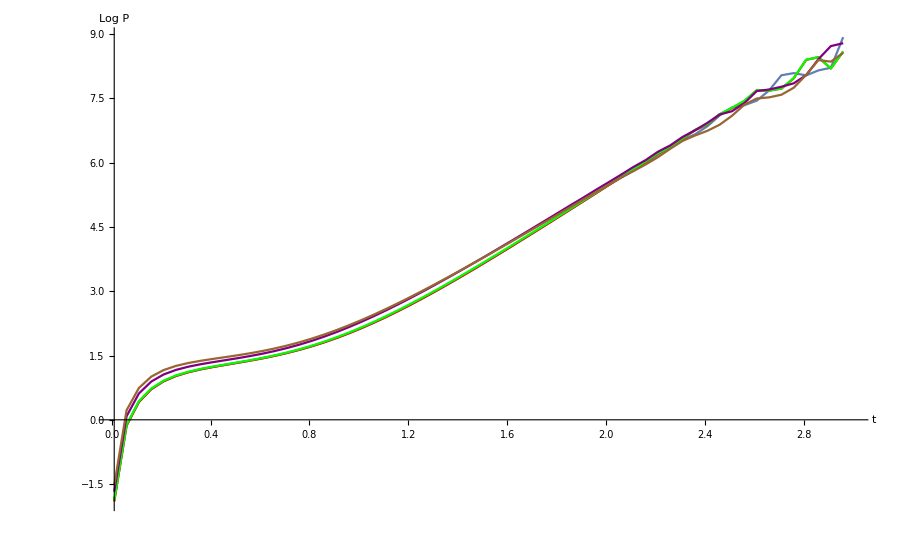

```mathematica
Show[
ListLinePlot[Table[{i,Abs[pz[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.75μextreme[1,1,0],1,1,0]]//Log},{i,0.01,3,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,10^(-4)],1,10^(-4)],0.75μextreme[1,1,10^(-4)],1,1,10^(-4)]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,10^(-2)],1,10^(-2)],0.75μextreme[1,1,10^(-2)],1,1,10^(-2)]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,0.1],1,0.1],0.75μextreme[1,1,0.1],1,1,0.1]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1qcrit[0.1,1,0.75μextreme[1,1,0.15],1,0.15],0.75μextreme[1,1,0.15],1,1,0.15]]//Log},{i,0.01,3,0.05}],PlotStyle->Brown],
PlotRange->{{0.01,3},All},AxesOrigin->{0.01,0},AxesLabel->{t,Log P}
]
```

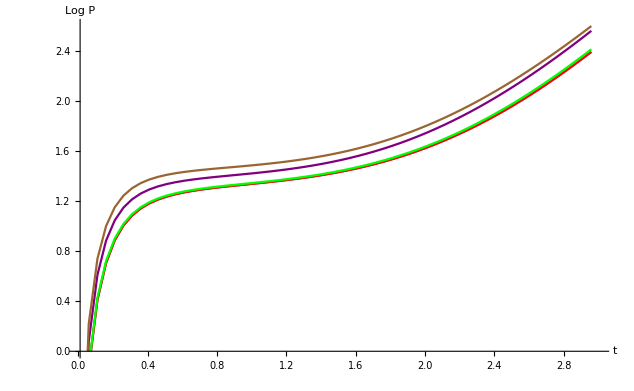

```mathematica
Show[
ListLinePlot[Table[{i,Abs[pz[i,1,0.7qcrit[0.1,1,0.75μextreme[1,1,0],1,0],0.75μextreme[1,1,0],1,1,0]]//Log},
{i,0.01,3,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,1,0.7qcrit[0.1,1,0.75μextreme[1,1,10^(-4)],1,10^(-4)],0.75μextreme[1,1,10^(-4)],1,1,10^(-4)]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pz[i,1,0.7qcrit[0.1,1,0.75μextreme[1,1,10^(-2)],1,10^(-2)],0.75μextreme[1,1,10^(-2)],1,1,10^(-2)]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[pz[i,1,0.7qcrit[0.1,1,0.75μextreme[1,1,0.1],1,0.1],0.75μextreme[1,1,0.1],1,1,0.1]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[pz[i,1,0.7qcrit[0.1,1,0.75μextreme[1,1,0.15],1,0.15],0.75μextreme[1,1,0.15],1,1,0.15]]//Log},{i,0.01,3,0.05}],PlotStyle->Brown],
PlotRange->{{0.01,3},All},AxesOrigin->{0.01,0},AxesLabel->{t,Log P}
]
```